1.1.3. Интерполяционная формула Лагранжа
б) Тригонометрическое интерполирование

```mathematica
Clear[f,h,knot(*узлы*),i,resF,g1,g2,g3]
f[x_]:=Sin[x]+Cos[x]+Sin[2 x - 6]^2;
(*Рассмотрим отрезок [-6;6]*)
h=2.4;
knot={};
Do[AppendTo[knot,-6+h*i],{i,0,5}]
knot
```

{-6.,-3.6,-1.2,1.2,3.6,6.}

```mathematica
knot⟦6⟧
f[knot⟦6⟧]
```

6.

0.758828

```mathematica
resF=Table[{knot⟦i⟧,f[knot⟦i⟧]},{i,6}]
```

{{-6.,1.80357},{-3.6,-0.103687},{-1.2,0.160658},{1.2,1.49022},{3.6,-0.470582},{6.,0.758828}}

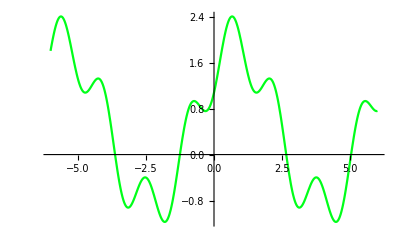

```mathematica
g1=Plot[f[x],{x,-6,6},PlotStyle->{Hue[0.35]}]
```

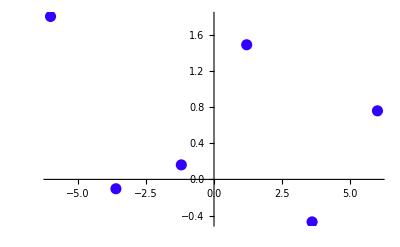

```mathematica
g2=ListPlot[resF,PlotStyle->{Hue[0.7],PointSize[0.02]}]
```

```mathematica
Clear[n,lagr,j]
n=5;
lagr[x_]:=Sum[f[knot⟦j⟧]*∏_(i=1)^n If[i==j,1,Sin[(x-knot⟦i⟧)/2]/Sin[(knot⟦j⟧-knot⟦i⟧)/2]],{j,1,5}];
```

```mathematica
Sum[f[knot⟦j⟧]*∏_(i=1)^n If[i==j,1,Sin[(x-knot⟦i⟧)/2]/Sin[(knot⟦j⟧-knot⟦i⟧)/2]],{j,1,5}]
```

6.49879 Sin[1/2 (-3.6+x)] Sin[1/2 (-1.2+x)] Sin[1/2 (1.2+x)] Sin[1/2 (3.6+x)]-0.39932 Sin[1/2 (-3.6+x)] Sin[1/2 (-1.2+x)] Sin[1/2 (1.2+x)] Sin[1/2 (6.+x)]+0.40535 Sin[1/2 (-3.6+x)] Sin[1/2 (-1.2+x)] Sin[1/2 (3.6+x)] Sin[1/2 (6.+x)]+5.73915 Sin[1/2 (-3.6+x)] Sin[1/2 (1.2+x)] Sin[1/2 (3.6+x)] Sin[1/2 (6.+x)]-1.69565 Sin[1/2 (-1.2+x)] Sin[1/2 (1.2+x)] Sin[1/2 (3.6+x)] Sin[1/2 (6.+x)]

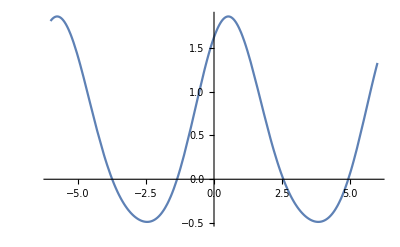

```mathematica
g3=Plot[lagr[x],{x,-6,6}]
```

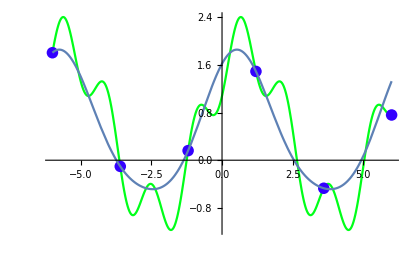

```mathematica
(*Наложим 3 графика друг на друга*)
Show[g1,g2,g3]
```